# 24: Eigenvalue Problems:

Eigenvalue eigenvector pairs of square matrices are next.  Your linear algebra class always wrote  
	A.v=λ v
your book likes to write A.x = λ x.  Whatever you want to call the eigenvector v it is important to realize that A is a map from a space into itself. An eigenvector is a special element of the space that preserves direction but not generally length under the map A.

For A∈ℂ^(m×m) any pair λ∈ℂ  and x∈ℂ^m (with ||x||≠0) satisfying
	A.x=λ x 
is an eigenpair for A:

λ is the eigenvalue associated with the eigenvector x.

The span of a set of eigenvectors is an eigenspace.

The set of all eigenvalues Λ(A) of A is the spectrum.

Finding eigenpairs is a non-linear problem!

Physical resonances are described by spectra and eigenspace

Eigenspaces let you “diagonalize” linear ODEs and other problems.

## Eigen Decomposition

With m linearly independent eigenvectors x_1,x_2,…,x_m the invertible matrix
	X=[x_1 | | | x_2 | | | … | | | x_m]
satisfies
	A.X=A.[x_1 | | | x_2 | | | … | | | x_m]=[A.x_1 | | | A.x_2 | | | … | | | A.x_m]=[λ_1 x_1 | | | λ_2 x_2 | | | … | | | λ_m x_m].
In other words with Λ the diagonal matrix of eigenvalues  
	A.X=X.Λ
This eigen decomposition of A and is normally written
	A=X.Λ.X^-1
In words: “A is diagonal under a change of basis”.  This is an orthogonal change of basis
	A=Q.Λ.Qᵀ
for real symmetric A.

## Geometric Multiplicity

One eigenvalue can have more than one linearly independent eigenvector.

The geometric multiplicity of an eigenvalue λ is the dimension of its eigenspace.

## Characteristic Polynomial

The characteristic polynomial of A is p_A(z)=det(z I - A)=z^m+…

Characteristic polynomial roots match eigenvalues

The algebraic multiplicity of an eigenvalue is the multiplicity of the characteristic polynomial root.

## Defective Eigenvalues and Matrices

An eigenvalue is defective if the multiplicities do not match.

A matrix is defective if it has a defective eigenvalue

Non-defective matrices have a full set of eigenvectors and are diagonalizable A=X.Λ.X^-1

The “Jordan Form” non-diagonalizable defective matrix 
	A=(3 | 1 | 0 | 0 | 0 | 0 | 0
0 | 3 | 1 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 | 1 | 0 | 0
0 | 0 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4)
Has three distinct eigenvalues 3,-2,4.

The eigenvalue 4 has geometric and algebraic multiplicity 2.

The eigenvalue -2 has geometric multiplicity 1 and algebraic multiplicity 2.

The eigenvalue 3 has geometric multiplicity 1 and algebraic multiplicity 3.

The Jordan Form (with the super-diagonal ones linking defective eigenvalues) is numerically unstable. As a result it is not computable in floating point arithmetic!

## Similarity Transformations

If Y∈ℂ^(m×m) is invertible then the eigenvalues of Y^-1.A.Y are the same as the eigenvalues of A.

If there is a unitary Q satisfying Q.A.Q^H then A is unitarily diagonalizable.

A matrix A is normal if A^H.A=A.A^H.  Normal matrices are unitarily diagonalizable.

Hermitian matrices (A=A^H ) are unitarily diagonalizable and have real eigenvalues.

Real symmetric matrices (A=A^ᵀ ) are have A=Q.Λ.Qᵀ with real eigenvalues.

## Schur Factorization

All square matrices have a Schur factorization A=Q.T.Q^H into a product of a Unitary Q and an Upper Triangular T. The eigenvalues of T are exposed on the diagonal!

## Locating Eigenvalues

There is a theorem that says that all the eigenvalues are within some disks.

“Every eigenvalue of A lies in at least one of the m circular disks with centers c_i=A⟦i,i⟧ and radius r_i=∑_(j≠i) |A⟦i,j⟧|. If k of the disks form a connected domain Ω disjoint from the other disks there are k eigenvalues in Ω.”

Here is a picture for the theorem.

```mathematica
GershgorignPic[A_]:=Module[{m=Length[A],c,r1,r2},
Graphics[{
Table[
c=ReIm[A⟦i,i⟧];
r1=Sum[Abs[A⟦i,j⟧],{j,1,i-1}]+Sum[Abs[A⟦i,j⟧],{j,i+1,m}];
r2=Sum[Abs[A⟦j,i⟧],{j,1,i-1}]+Sum[Abs[A⟦i,j⟧],{j,i+1,m}];
{Hue[i/m],Opacity[0.2],EdgeForm[Hue[i/m]],
Disk[c,Min[r1,r2],{0,π/2}],
Disk[c,Min[r1,r2],{π/2,π}],
Disk[c,Min[r1,r2],{π,3π/2}],
Disk[c,Min[r1,r2],{3π/2,2π}]},
{i,m}],
Point[ReIm[Eigenvalues[A]]]},
Frame->True,
FrameLabel->{"re(λ)","im(λ)"},
GridLines->Automatic]
]
```

Lets look at the theorem.

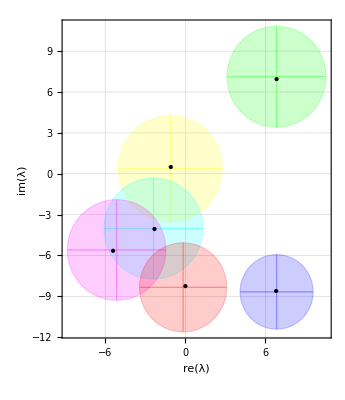

```mathematica
m=6;
A=RandomComplex[{-1-I,1+I},{m,m}]; A =A+10 DiagonalMatrix[RandomComplex[{-1-1I,1+1 I},m]];
λs=Eigenvalues[A];
GershgorignPic[A]
```

## Computing Eigenvalues

We compute eigenvalues by building one of the above decompositions and reading off the eigenvalues.

## Oldest Eigenvalue Algorithm: Jacobi

Before the word “matrix” existed Jacobi needed to compute what would be called the eigenvalues of a real symmetric 7×7 matrix: there were only seven known planets at the time! He invented what is now called the Jacobi method!

#### 2×2 Diagonalization

We can diagonalize a symmetric 2 by 2 matrix using the Givens rotation (p1 | p2
-p2 | p1).   Lets work out the recipe!

```mathematica
AHat=({{p1, p2}, {-p2, p1}}).({{a11, a12}, {a12, a22}}).({{p1, -p2}, {p2, p1}});
MatrixForm[AHat]
```

(p1 (a11 p1+a12 p2)+p2 (a12 p1+a22 p2) | -p2 (a11 p1+a12 p2)+p1 (a12 p1+a22 p2)
p1 (a12 p1-a11 p2)+p2 (a22 p1-a12 p2) | -p2 (a12 p1-a11 p2)+p1 (a22 p1-a12 p2))

There are two values of p1 that work for any p2! Of course, we need to check that the expression under the square root is not negative if we want a real computation.

```mathematica
Solve[AHat⟦1,2⟧==0,p1]
```

{{p1→(a11 p2-a22 p2-√(a11^2+4 a12^2-2 a11 a22+a22^2) p2)/(2 a12)},{p1→(a11 p2-a22 p2+√(a11^2+4 a12^2-2 a11 a22+a22^2) p2)/(2 a12)}}

It is OK since a11^2+4 a12^2-2 a11 a22+a22^2=(a11-a22)^2+4 a12^2.  In practice, we should choose which solution we use carefully.  For now I am going to use the first one! Remember for the Givens matrices we need ||{p1,p2}||=1.

```mathematica
JMat[{{a11_,a12_},{a21_,a22_}}]:=Module[{p1,p2=1},
p1=(a11-a22-√((a11-a22)^2+4 a12^2))/(2 a12);
{p1,p2}=Normalize[{p1,p2}];
({{p1, p2}, {-p2, p1}})
]
```

As always test

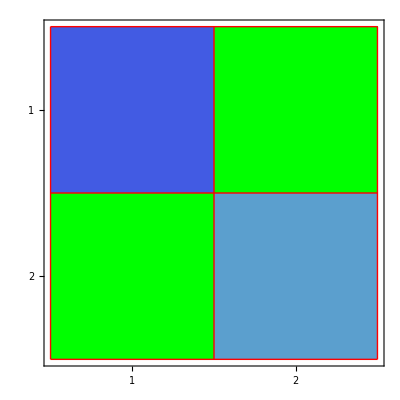

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
G=JMat[A];
GAGt=G.A.Gᵀ;
Map[MatrixForm,{G.Gᵀ,GAGt}];
MatrixPlot[Chop[GAGt],PlotLegends->Automatic]
```

To use this in a larger matrix we target a specific entry {i,j} and embed the appropriate tiny rotation in the identity matrix.

```mathematica
SetAttributes[BigJ,HoldFirst];
BigJ[A_,{i_,j_}]:=Module[{m=Length[A],G},
G=IdentityMatrix[m];
G⟦{i,j},{i,j}⟧=JMat[A⟦{i,j},{i,j}⟧];
G
]
```

As always test!

```mathematica
m=7;
A=RandomReal[{-1,1},{m,m}]; A= A + Aᵀ;
{i,j}={1,5};
G=BigJ[A,{i,j}];
GAGt=G.A.Gᵀ;
TabView[Map[MatrixPlot,Chop[{GAGt,G,G.Gᵀ,A}]]]
```

1234

So lets try to string a few of these together. It works just the way we expect if we are careful not to overlap!

```mathematica
m=7;
A=A0=RandomReal[{-1,1},{m,m}]; A= A + Aᵀ;
Data=Table[
G=BigJ[A,ij];
A=G.A.Gᵀ,
{ij,{{1,2},{3,4},{5,6}}}];
SetOptions[MatrixPlot, 
ColorRules->{0->Green},Mesh->All,MeshStyle->Red];
TabView[Map[MatrixPlot,Chop[Data]]]
```

123

If we overlap zeros that were made earlier get messed up.

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
Data=Table[
G=BigJ[A,ij];
A=G.A.Gᵀ,
{ij,{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7}}}];
SetOptions[MatrixPlot, ColorRules->{0->Green},Mesh->All,MeshStyle->Red];
TabView[Map[MatrixPlot,Chop[Data]]]
MatrixForm[A]
```

123456

(-2.99909 | -1.01964 | 0.270905 | -0.560693 | -0.588452 | 0.0266957 | 1.21967×10^-17
-1.01964 | 1.2561 | 0.892419 | 1.30641 | -0.439861 | -0.5464 | 1.03099
0.270905 | 0.892419 | 1.61535 | -0.845484 | 0.582547 | -0.358338 | 0.0700772
-0.560693 | 1.30641 | -0.845484 | 1.73832 | -0.286041 | -0.398054 | 0.0561176
-0.588452 | -0.439861 | 0.582547 | -0.286041 | 1.72542 | -0.591375 | -0.587935
0.0266957 | -0.5464 | -0.358338 | -0.398054 | -0.591375 | 1.33971 | -0.464168
-1.04083×10^-17 | 1.03099 | 0.0700772 | 0.0561176 | -0.587935 | -0.464168 | -0.492839)

Jacobi (or more likely one of his helpers aka computers or computes) was doing this by hand and would have been painstakingly updating a block of numbers.

You would like to be done as fast as possible.

You can do any of the entries.

Which one should you do?

Jacobi’s plan was “do the big ones first!”  This assumes that arithmetic is slow (it was then) and that it is fast (true for a small matrix) to find the biggest entry.

```mathematica
SetAttributes[JacobiStep, HoldFirst]
JacobiStep[A_]:= Module[{AbsA=Abs[UpperTriangularize[A,1]],ij,G},
(* Find the largest non-diagonal entry *)
ij=Position[AbsA,Max[AbsA]]⟦1⟧;
(* Compute the Jacobi/Given rotation zapping the biggest entry *)
G=BigJ[A,ij];
(* Update A in place *)
A=G.A.Gᵀ;
(* No need to return anything! *)
]
```

As always test.

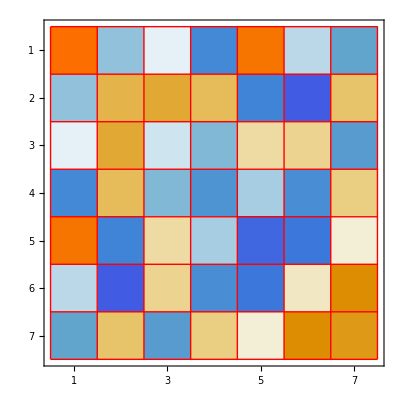
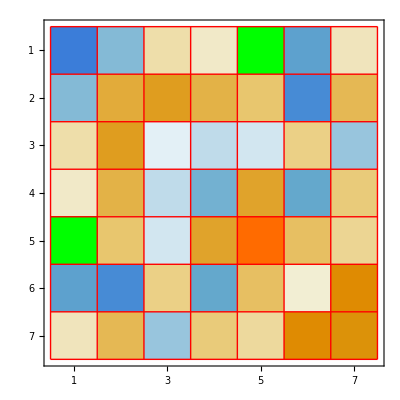

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
JacobiStep[A]
Map[MatrixPlot,Chop[{A0,A}]]
```

Now we can do a bunch and know that we are always targeting (and zeroing) large entries! This ensures it always makes progress and that it converges fast at the end!  Of course, copying and pasting is not a good plan! After a few steps the off-diagonal is looking fairly pale!

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
TabView[{
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]]}]
```

12345678

Automation is a good thing!

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
MaxIter=16;
TabView[Table[
JacobiStep[A];MatrixPlot[Chop[A]],
{MaxIter}]]
```

12345678910111213141516

Animation is a good thing!

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
MaxIter=89;
ListAnimate[Table[
JacobiStep[A];MatrixPlot[Chop[A],PlotLabel->i],
{i,MaxIter}],8]
```

Things to note, something about our choices is pushing the negative eigenvalues up and the positive eigenvalues down!  Other choices will do other things! The common choice is to push the big (either positive or negative eigenvalues up) and the small eigenvalues down!

This algorithm has more parallelism than the standard “QR” Francis algorithm we are going to learn.  It has a developed “very quaternionic” G4 version that block diagonalizes symmetric matrices.  I am working on an alternative G4 and a G8 algorithm that make progress with a simple plan of “move the big entries up”.